### Equilibrium & Eigenvalues

```mathematica
Remove["Global`*"];
Clear["Global`*"];

numeriana[α_,β_]:=Do[

q=0.3;
m=0.2;
η = m/q;

f[i_]:=α((1-Exp[-β i/ino])/(1+Exp[-β i/ino]));

For[i=1,i≤ino,i++,
Subscript[d0, i]=(q f[i](1-∑_(j=1)^i Subscript[pn, j])-q ∑_(j=1)^(i-1) Subscript[pn, j] f[j]-m)Subscript[pn, i];
];

Subscript[sp, 0]=0;
Subscript[spf, 0]=0;
For[i=1,i≤ino,i++,
If[f[i]≤η ,Subscript[pp, i]=0,Subscript[pp, i]=1-Subscript[sp, i-1]-1/f[i](η+Subscript[spf, i-1])];
If[Subscript[pp, i]<0,Subscript[pp, i]=0];
Subscript[sp, i]=Subscript[sp, i-1]+Subscript[pp, i];
Subscript[spf, i]=Subscript[spf, i-1]+Subscript[pp, i] f[i];
];
];
```

Remove::rmnsm: "Global`*"に合致するシンボルはありません．

```mathematica
ino=80;
minlog=-5;

αmin=1;
αmax=5;
βmin=1;
βmax=20;

grno=25;

For[k=1,k≤grno,k++,
αα=αmin+(αmax-αmin)(k-1)/grno;
For[j=1,j≤grno,j++,
ββ=βmin+(βmax-βmin)(j-1)/grno;

numeriana[αα,ββ];
total=Sum[Subscript[pp, i],{i,1,ino}];
If[total≠0,
tas=Sort[Table[{i,Subscript[pp, i]/total},{i,1,ino}],#1[[2]]>#2[[2]]&];
tas2=Split[tas,#2[[2]]>10^minlog&][[1]];
	(* tas2 ... (competitiveness, frequency) in rank order *)
detspno[k][j]=Length[tas2];
biomass[k][j]=total;
,
detspno[k][j]=0;
biomass[k][j]=0;
];

(*
Print[k," ",j," ",inita];
Print[detspno[k][j]];
Print[biomass[k][j]];
*)
];
];
```

```mathematica
dlist=Flatten[Table[{N[αmin+(αmax-αmin)(k-1)/grno],N[βmin+(βmax-βmin)(j-1)/grno],detspno[k][j]},{k,1,grno},{j,1,grno}],1]
blist=Flatten[Table[{N[αmin+(αmax-αmin)(k-1)/grno],N[βmin+(βmax-βmin)(j-1)/grno],biomass[k][j]},{k,1,grno},{j,1,grno}],1]
```

{{1.,1.,0},{1.,1.76,7},{1.,2.52,21},{1.,3.28,32},{1.,4.04,31},{1.,4.8,33},{1.,5.56,32},{1.,6.32,45},{1.,7.08,38},{1.,7.84,45},{1.,8.6,43},{1.,9.36,41},{1.,10.12,45},{1.,10.88,39},{1.,11.64,41},{1.,12.4,42},{1.,13.16,39},{1.,13.92,36},{1.,14.68,35},{1.,15.44,35},{1.,16.2,32},{1.,16.96,31},{1.,17.72,28},{1.,18.48,27},{1.,19.24,29},{1.16,1.,0},{1.16,1.76,21},{1.16,2.52,39},{1.16,3.28,29},{1.16,4.04,29},{1.16,4.8,36},{1.16,5.56,39},{1.16,6.32,50},{1.16,7.08,44},{1.16,7.84,45},{1.16,8.6,43},{1.16,9.36,41},{1.16,10.12,44},{1.16,10.88,45},{1.16,11.64,39},{1.16,12.4,43},{1.16,13.16,38},{1.16,13.92,47},{1.16,14.68,31},{1.16,15.44,32},{1.16,16.2,36},{1.16,16.96,29},{1.16,17.72,30},{1.16,18.48,29},{1.16,19.24,30},{1.32,1.,0},{1.32,1.76,30},{1.32,2.52,36},{1.32,3.28,39},{1.32,4.04,35},{1.32,4.8,55},{1.32,5.56,42},{1.32,6.32,43},{1.32,7.08,50},{1.32,7.84,46},{1.32,8.6,45},{1.32,9.36,52},{1.32,10.12,44},{1.32,10.88,43},{1.32,11.64,45},{1.32,12.4,39},{1.32,13.16,40},{1.32,13.92,36},{1.32,14.68,33},{1.32,15.44,30},{1.32,16.2,34},{1.32,16.96,29},{1.32,17.72,29},{1.32,18.48,27},{1.32,19.24,28},{1.48,1.,3},{1.48,1.76,22},{1.48,2.52,35},{1.48,3.28,42},{1.48,4.04,41},{1.48,4.8,43},{1.48,5.56,42},{1.48,6.32,42},{1.48,7.08,46},{1.48,7.84,44},{1.48,8.6,44},{1.48,9.36,48},{1.48,10.12,47},{1.48,10.88,41},{1.48,11.64,39},{1.48,12.4,38},{1.48,13.16,36},{1.48,13.92,37},{1.48,14.68,33},{1.48,15.44,31},{1.48,16.2,31},{1.48,16.96,35},{1.48,17.72,28},{1.48,18.48,28},{1.48,19.24,29},{1.64,1.,7},{1.64,1.76,31},{1.64,2.52,47},{1.64,3.28,38},{1.64,4.04,40},{1.64,4.8,49},{1.64,5.56,48},{1.64,6.32,45},{1.64,7.08,48},{1.64,7.84,45},{1.64,8.6,43},{1.64,9.36,47},{1.64,10.12,45},{1.64,10.88,44},{1.64,11.64,41},{1.64,12.4,44},{1.64,13.16,33},{1.64,13.92,37},{1.64,14.68,34},{1.64,15.44,36},{1.64,16.2,29},{1.64,16.96,29},{1.64,17.72,29},{1.64,18.48,26},{1.64,19.24,31},{1.8,1.,18},{1.8,1.76,45},{1.8,2.52,41},{1.8,3.28,32},{1.8,4.04,51},{1.8,4.8,41},{1.8,5.56,41},{1.8,6.32,44},{1.8,7.08,46},{1.8,7.84,43},{1.8,8.6,49},{1.8,9.36,47},{1.8,10.12,39},{1.8,10.88,44},{1.8,11.64,42},{1.8,12.4,38},{1.8,13.16,37},{1.8,13.92,36},{1.8,14.68,33},{1.8,15.44,31},{1.8,16.2,29},{1.8,16.96,29},{1.8,17.72,31},{1.8,18.48,30},{1.8,19.24,28},{1.96,1.,24},{1.96,1.76,32},{1.96,2.52,58},{1.96,3.28,42},{1.96,4.04,42},{1.96,4.8,47},{1.96,5.56,43},{1.96,6.32,45},{1.96,7.08,43},{1.96,7.84,49},{1.96,8.6,49},{1.96,9.36,42},{1.96,10.12,47},{1.96,10.88,43},{1.96,11.64,40},{1.96,12.4,46},{1.96,13.16,36},{1.96,13.92,34},{1.96,14.68,31},{1.96,15.44,30},{1.96,16.2,33},{1.96,16.96,29},{1.96,17.72,28},{1.96,18.48,28},{1.96,19.24,30},{2.12,1.,19},{2.12,1.76,51},{2.12,2.52,44},{2.12,3.28,42},{2.12,4.04,36},{2.12,4.8,47},{2.12,5.56,52},{2.12,6.32,46},{2.12,7.08,49},{2.12,7.84,43},{2.12,8.6,43},{2.12,9.36,51},{2.12,10.12,45},{2.12,10.88,42},{2.12,11.64,43},{2.12,12.4,38},{2.12,13.16,37},{2.12,13.92,35},{2.12,14.68,38},{2.12,15.44,33},{2.12,16.2,28},{2.12,16.96,29},{2.12,17.72,30},{2.12,18.48,26},{2.12,19.24,27},{2.28,1.,28},{2.28,1.76,51},{2.28,2.52,36},{2.28,3.28,43},{2.28,4.04,46},{2.28,4.8,44},{2.28,5.56,50},{2.28,6.32,47},{2.28,7.08,48},{2.28,7.84,45},{2.28,8.6,49},{2.28,9.36,45},{2.28,10.12,47},{2.28,10.88,44},{2.28,11.64,41},{2.28,12.4,38},{2.28,13.16,37},{2.28,13.92,36},{2.28,14.68,34},{2.28,15.44,31},{2.28,16.2,31},{2.28,16.96,29},{2.28,17.72,26},{2.28,18.48,29},{2.28,19.24,30},{2.44,1.,27},{2.44,1.76,55},{2.44,2.52,44},{2.44,3.28,47},{2.44,4.04,47},{2.44,4.8,45},{2.44,5.56,37},{2.44,6.32,48},{2.44,7.08,49},{2.44,7.84,47},{2.44,8.6,42},{2.44,9.36,43},{2.44,10.12,47},{2.44,10.88,38},{2.44,11.64,41},{2.44,12.4,38},{2.44,13.16,35},{2.44,13.92,36},{2.44,14.68,34},{2.44,15.44,31},{2.44,16.2,31},{2.44,16.96,29},{2.44,17.72,31},{2.44,18.48,27},{2.44,19.24,26},{2.6,1.,21},{2.6,1.76,38},{2.6,2.52,48},{2.6,3.28,47},{2.6,4.04,52},{2.6,4.8,48},{2.6,5.56,57},{2.6,6.32,48},{2.6,7.08,45},{2.6,7.84,47},{2.6,8.6,46},{2.6,9.36,47},{2.6,10.12,44},{2.6,10.88,39},{2.6,11.64,46},{2.6,12.4,41},{2.6,13.16,38},{2.6,13.92,35},{2.6,14.68,33},{2.6,15.44,31},{2.6,16.2,33},{2.6,16.96,29},{2.6,17.72,28},{2.6,18.48,27},{2.6,19.24,26},{2.76,1.,41},{2.76,1.76,55},{2.76,2.52,51},{2.76,3.28,43},{2.76,4.04,46},{2.76,4.8,39},{2.76,5.56,46},{2.76,6.32,46},{2.76,7.08,52},{2.76,7.84,42},{2.76,8.6,52},{2.76,9.36,48},{2.76,10.12,43},{2.76,10.88,44},{2.76,11.64,41},{2.76,12.4,39},{2.76,13.16,39},{2.76,13.92,32},{2.76,14.68,34},{2.76,15.44,38},{2.76,16.2,32},{2.76,16.96,31},{2.76,17.72,27},{2.76,18.48,27},{2.76,19.24,27},{2.92,1.,31},{2.92,1.76,39},{2.92,2.52,47},{2.92,3.28,48},{2.92,4.04,46},{2.92,4.8,40},{2.92,5.56,50},{2.92,6.32,47},{2.92,7.08,48},{2.92,7.84,49},{2.92,8.6,47},{2.92,9.36,45},{2.92,10.12,50},{2.92,10.88,43},{2.92,11.64,38},{2.92,12.4,42},{2.92,13.16,37},{2.92,13.92,35},{2.92,14.68,37},{2.92,15.44,32},{2.92,16.2,31},{2.92,16.96,26},{2.92,17.72,27},{2.92,18.48,28},{2.92,19.24,28},{3.08,1.,32},{3.08,1.76,39},{3.08,2.52,34},{3.08,3.28,44},{3.08,4.04,48},{3.08,4.8,49},{3.08,5.56,48},{3.08,6.32,53},{3.08,7.08,43},{3.08,7.84,51},{3.08,8.6,44},{3.08,9.36,48},{3.08,10.12,48},{3.08,10.88,39},{3.08,11.64,38},{3.08,12.4,36},{3.08,13.16,34},{3.08,13.92,37},{3.08,14.68,32},{3.08,15.44,32},{3.08,16.2,30},{3.08,16.96,30},{3.08,17.72,29},{3.08,18.48,29},{3.08,19.24,27},{3.24,1.,47},{3.24,1.76,36},{3.24,2.52,44},{3.24,3.28,40},{3.24,4.04,49},{3.24,4.8,46},{3.24,5.56,47},{3.24,6.32,47},{3.24,7.08,47},{3.24,7.84,46},{3.24,8.6,39},{3.24,9.36,53},{3.24,10.12,48},{3.24,10.88,42},{3.24,11.64,37},{3.24,12.4,38},{3.24,13.16,42},{3.24,13.92,34},{3.24,14.68,35},{3.24,15.44,32},{3.24,16.2,31},{3.24,16.96,37},{3.24,17.72,28},{3.24,18.48,26},{3.24,19.24,28},{3.4,1.,38},{3.4,1.76,41},{3.4,2.52,51},{3.4,3.28,49},{3.4,4.04,47},{3.4,4.8,47},{3.4,5.56,42},{3.4,6.32,42},{3.4,7.08,53},{3.4,7.84,45},{3.4,8.6,50},{3.4,9.36,43},{3.4,10.12,42},{3.4,10.88,37},{3.4,11.64,40},{3.4,12.4,43},{3.4,13.16,36},{3.4,13.92,34},{3.4,14.68,31},{3.4,15.44,31},{3.4,16.2,34},{3.4,16.96,27},{3.4,17.72,27},{3.4,18.48,29},{3.4,19.24,29},{3.56,1.,46},{3.56,1.76,43},{3.56,2.52,42},{3.56,3.28,48},{3.56,4.04,67},{3.56,4.8,49},{3.56,5.56,56},{3.56,6.32,46},{3.56,7.08,49},{3.56,7.84,46},{3.56,8.6,55},{3.56,9.36,48},{3.56,10.12,48},{3.56,10.88,41},{3.56,11.64,45},{3.56,12.4,37},{3.56,13.16,37},{3.56,13.92,32},{3.56,14.68,35},{3.56,15.44,34},{3.56,16.2,30},{3.56,16.96,30},{3.56,17.72,28},{3.56,18.48,28},{3.56,19.24,33},{3.72,1.,30},{3.72,1.76,64},{3.72,2.52,69},{3.72,3.28,49},{3.72,4.04,49},{3.72,4.8,49},{3.72,5.56,45},{3.72,6.32,53},{3.72,7.08,46},{3.72,7.84,48},{3.72,8.6,49},{3.72,9.36,47},{3.72,10.12,42},{3.72,10.88,40},{3.72,11.64,40},{3.72,12.4,36},{3.72,13.16,33},{3.72,13.92,34},{3.72,14.68,38},{3.72,15.44,31},{3.72,16.2,29},{3.72,16.96,28},{3.72,17.72,31},{3.72,18.48,31},{3.72,19.24,27},{3.88,1.,40},{3.88,1.76,44},{3.88,2.52,45},{3.88,3.28,58},{3.88,4.04,48},{3.88,4.8,49},{3.88,5.56,50},{3.88,6.32,50},{3.88,7.08,45},{3.88,7.84,58},{3.88,8.6,43},{3.88,9.36,46},{3.88,10.12,42},{3.88,10.88,51},{3.88,11.64,40},{3.88,12.4,35},{3.88,13.16,38},{3.88,13.92,38},{3.88,14.68,33},{3.88,15.44,30},{3.88,16.2,29},{3.88,16.96,30},{3.88,17.72,33},{3.88,18.48,29},{3.88,19.24,27},{4.04,1.,54},{4.04,1.76,43},{4.04,2.52,59},{4.04,3.28,45},{4.04,4.04,53},{4.04,4.8,56},{4.04,5.56,48},{4.04,6.32,47},{4.04,7.08,47},{4.04,7.84,50},{4.04,8.6,47},{4.04,9.36,46},{4.04,10.12,47},{4.04,10.88,43},{4.04,11.64,36},{4.04,12.4,39},{4.04,13.16,40},{4.04,13.92,34},{4.04,14.68,32},{4.04,15.44,30},{4.04,16.2,30},{4.04,16.96,36},{4.04,17.72,29},{4.04,18.48,28},{4.04,19.24,27},{4.2,1.,55},{4.2,1.76,66},{4.2,2.52,46},{4.2,3.28,47},{4.2,4.04,49},{4.2,4.8,51},{4.2,5.56,53},{4.2,6.32,44},{4.2,7.08,52},{4.2,7.84,44},{4.2,8.6,50},{4.2,9.36,47},{4.2,10.12,51},{4.2,10.88,40},{4.2,11.64,37},{4.2,12.4,39},{4.2,13.16,39},{4.2,13.92,33},{4.2,14.68,33},{4.2,15.44,30},{4.2,16.2,37},{4.2,16.96,30},{4.2,17.72,28},{4.2,18.48,27},{4.2,19.24,25},{4.36,1.,52},{4.36,1.76,42},{4.36,2.52,41},{4.36,3.28,73},{4.36,4.04,45},{4.36,4.8,46},{4.36,5.56,51},{4.36,6.32,45},{4.36,7.08,52},{4.36,7.84,42},{4.36,8.6,45},{4.36,9.36,51},{4.36,10.12,43},{4.36,10.88,43},{4.36,11.64,39},{4.36,12.4,50},{4.36,13.16,33},{4.36,13.92,32},{4.36,14.68,32},{4.36,15.44,33},{4.36,16.2,31},{4.36,16.96,29},{4.36,17.72,29},{4.36,18.48,27},{4.36,19.24,24},{4.52,1.,38},{4.52,1.76,67},{4.52,2.52,53},{4.52,3.28,48},{4.52,4.04,45},{4.52,4.8,49},{4.52,5.56,49},{4.52,6.32,48},{4.52,7.08,47},{4.52,7.84,47},{4.52,8.6,47},{4.52,9.36,53},{4.52,10.12,43},{4.52,10.88,39},{4.52,11.64,39},{4.52,12.4,40},{4.52,13.16,32},{4.52,13.92,33},{4.52,14.68,36},{4.52,15.44,34},{4.52,16.2,29},{4.52,16.96,28},{4.52,17.72,27},{4.52,18.48,25},{4.52,19.24,25},{4.68,1.,38},{4.68,1.76,34},{4.68,2.52,46},{4.68,3.28,47},{4.68,4.04,50},{4.68,4.8,47},{4.68,5.56,46},{4.68,6.32,44},{4.68,7.08,49},{4.68,7.84,46},{4.68,8.6,50},{4.68,9.36,50},{4.68,10.12,44},{4.68,10.88,42},{4.68,11.64,45},{4.68,12.4,38},{4.68,13.16,35},{4.68,13.92,34},{4.68,14.68,37},{4.68,15.44,30},{4.68,16.2,28},{4.68,16.96,28},{4.68,17.72,28},{4.68,18.48,28},{4.68,19.24,27},{4.84,1.,40},{4.84,1.76,57},{4.84,2.52,49},{4.84,3.28,50},{4.84,4.04,59},{4.84,4.8,49},{4.84,5.56,45},{4.84,6.32,54},{4.84,7.08,47},{4.84,7.84,47},{4.84,8.6,51},{4.84,9.36,48},{4.84,10.12,40},{4.84,10.88,42},{4.84,11.64,39},{4.84,12.4,36},{4.84,13.16,35},{4.84,13.92,35},{4.84,14.68,35},{4.84,15.44,32},{4.84,16.2,30},{4.84,16.96,28},{4.84,17.72,27},{4.84,18.48,25},{4.84,19.24,28}}

{{1.,1.,0},{1.,1.76,0.0319699},{1.,2.52,0.117154},{1.,3.28,0.153514},{1.,4.04,0.169046},{1.,4.8,0.177147},{1.,5.56,0.180564},{1.,6.32,0.182033},{1.,7.08,0.182821},{1.,7.84,0.183185},{1.,8.6,0.18337},{1.,9.36,0.183433},{1.,10.12,0.183475},{1.,10.88,0.183488},{1.,11.64,0.183497},{1.,12.4,0.1835},{1.,13.16,0.183502},{1.,13.92,0.183503},{1.,14.68,0.183503},{1.,15.44,0.183503},{1.,16.2,0.183503},{1.,16.96,0.183503},{1.,17.72,0.183503},{1.,18.48,0.183503},{1.,19.24,0.183503},{1.16,1.,0},{1.16,1.76,0.0997849},{1.16,2.52,0.178889},{1.16,3.28,0.212823},{1.16,4.04,0.228442},{1.16,4.8,0.235638},{1.16,5.56,0.239174},{1.16,6.32,0.240648},{1.16,7.08,0.241317},{1.16,7.84,0.241631},{1.16,8.6,0.241762},{1.16,9.36,0.241845},{1.16,10.12,0.241872},{1.16,10.88,0.241888},{1.16,11.64,0.241896},{1.16,12.4,0.241899},{1.16,13.16,0.241901},{1.16,13.92,0.241901},{1.16,14.68,0.241902},{1.16,15.44,0.241902},{1.16,16.2,0.241902},{1.16,16.96,0.241902},{1.16,17.72,0.241902},{1.16,18.48,0.241902},{1.16,19.24,0.241902},{1.32,1.,0},{1.32,1.76,0.156431},{1.32,2.52,0.231594},{1.32,3.28,0.26318},{1.32,4.04,0.276744},{1.32,4.8,0.283806},{1.32,5.56,0.286592},{1.32,6.32,0.288052},{1.32,7.08,0.288783},{1.32,7.84,0.289077},{1.32,8.6,0.2892},{1.32,9.36,0.289277},{1.32,10.12,0.289306},{1.32,10.88,0.289318},{1.32,11.64,0.289325},{1.32,12.4,0.289328},{1.32,13.16,0.28933},{1.32,13.92,0.28933},{1.32,14.68,0.289331},{1.32,15.44,0.289331},{1.32,16.2,0.289331},{1.32,16.96,0.289331},{1.32,17.72,0.289331},{1.32,18.48,0.289331},{1.32,19.24,0.289331},{1.48,1.,0.0145601},{1.48,1.76,0.201531},{1.48,2.52,0.274364},{1.48,3.28,0.303097},{1.48,4.04,0.317517},{1.48,4.8,0.323316},{1.48,5.56,0.326269},{1.48,6.32,0.327636},{1.48,7.08,0.328331},{1.48,7.84,0.32858},{1.48,8.6,0.328733},{1.48,9.36,0.328787},{1.48,10.12,0.328817},{1.48,10.88,0.328833},{1.48,11.64,0.328839},{1.48,12.4,0.328841},{1.48,13.16,0.328843},{1.48,13.92,0.328843},{1.48,14.68,0.328844},{1.48,15.44,0.328844},{1.48,16.2,0.328844},{1.48,16.96,0.328844},{1.48,17.72,0.328844},{1.48,18.48,0.328844},{1.48,19.24,0.328844},{1.64,1.,0.0670706},{1.64,1.76,0.244398},{1.64,2.52,0.310621},{1.64,3.28,0.339007},{1.64,4.04,0.351691},{1.64,4.8,0.357173},{1.64,5.56,0.359976},{1.64,6.32,0.361362},{1.64,7.08,0.361887},{1.64,7.84,0.362195},{1.64,8.6,0.362306},{1.64,9.36,0.362374},{1.64,10.12,0.362401},{1.64,10.88,0.362411},{1.64,11.64,0.362418},{1.64,12.4,0.362421},{1.64,13.16,0.362422},{1.64,13.92,0.362423},{1.64,14.68,0.362423},{1.64,15.44,0.362423},{1.64,16.2,0.362423},{1.64,16.96,0.362423},{1.64,17.72,0.362423},{1.64,18.48,0.362423},{1.64,19.24,0.362423},{1.8,1.,0.105276},{1.8,1.76,0.278751},{1.8,2.52,0.342016},{1.8,3.28,0.369041},{1.8,4.04,0.381148},{1.8,4.8,0.386685},{1.8,5.56,0.389241},{1.8,6.32,0.39033},{1.8,7.08,0.39095},{1.8,7.84,0.39118},{1.8,8.6,0.39132},{1.8,9.36,0.391373},{1.8,10.12,0.391395},{1.8,10.88,0.391408},{1.8,11.64,0.391415},{1.8,12.4,0.391417},{1.8,13.16,0.391418},{1.8,13.92,0.391419},{1.8,14.68,0.391419},{1.8,15.44,0.391419},{1.8,16.2,0.391419},{1.8,16.96,0.391419},{1.8,17.72,0.391419},{1.8,18.48,0.391419},{1.8,19.24,0.391419},{1.96,1.,0.145582},{1.96,1.76,0.306107},{1.96,2.52,0.36843},{1.96,3.28,0.395368},{1.96,4.04,0.406459},{1.96,4.8,0.411987},{1.96,5.56,0.41455},{1.96,6.32,0.415817},{1.96,7.08,0.416297},{1.96,7.84,0.416582},{1.96,8.6,0.416693},{1.96,9.36,0.416739},{1.96,10.12,0.416765},{1.96,10.88,0.416779},{1.96,11.64,0.416784},{1.96,12.4,0.416786},{1.96,13.16,0.416787},{1.96,13.92,0.416788},{1.96,14.68,0.416788},{1.96,15.44,0.416788},{1.96,16.2,0.416788},{1.96,16.96,0.416788},{1.96,17.72,0.416788},{1.96,18.48,0.416788},{1.96,19.24,0.416788},{2.12,1.,0.175083},{2.12,1.76,0.333202},{2.12,2.52,0.393664},{2.12,3.28,0.417715},{2.12,4.04,0.429773},{2.12,4.8,0.434881},{2.12,5.56,0.437221},{2.12,6.32,0.438223},{2.12,7.08,0.438795},{2.12,7.84,0.439028},{2.12,8.6,0.439126},{2.12,9.36,0.43918},{2.12,10.12,0.439208},{2.12,10.88,0.439219},{2.12,11.64,0.439223},{2.12,12.4,0.439226},{2.12,13.16,0.439227},{2.12,13.92,0.439227},{2.12,14.68,0.439228},{2.12,15.44,0.439228},{2.12,16.2,0.439228},{2.12,16.96,0.439228},{2.12,17.72,0.439228},{2.12,18.48,0.439228},{2.12,19.24,0.439228},{2.28,1.,0.204557},{2.28,1.76,0.359139},{2.28,2.52,0.415321},{2.28,3.28,0.439365},{2.28,4.04,0.449687},{2.28,4.8,0.454808},{2.28,5.56,0.457317},{2.28,6.32,0.458294},{2.28,7.08,0.458849},{2.28,7.84,0.459049},{2.28,8.6,0.459163},{2.28,9.36,0.459221},{2.28,10.12,0.459243},{2.28,10.88,0.459252},{2.28,11.64,0.459257},{2.28,12.4,0.45926},{2.28,13.16,0.459261},{2.28,13.92,0.459262},{2.28,14.68,0.459262},{2.28,15.44,0.459262},{2.28,16.2,0.459262},{2.28,16.96,0.459262},{2.28,17.72,0.459262},{2.28,18.48,0.459262},{2.28,19.24,0.459262},{2.44,1.,0.235118},{2.44,1.76,0.379526},{2.44,2.52,0.433401},{2.44,3.28,0.457241},{2.44,4.04,0.468472},{2.44,4.8,0.47324},{2.44,5.56,0.475285},{2.44,6.32,0.476421},{2.44,7.08,0.476855},{2.44,7.84,0.477086},{2.44,8.6,0.477206},{2.44,9.36,0.477252},{2.44,10.12,0.477271},{2.44,10.88,0.477282},{2.44,11.64,0.477287},{2.44,12.4,0.477289},{2.44,13.16,0.477291},{2.44,13.92,0.477291},{2.44,14.68,0.477291},{2.44,15.44,0.477292},{2.44,16.2,0.477292},{2.44,16.96,0.477292},{2.44,17.72,0.477292},{2.44,18.48,0.477292},{2.44,19.24,0.477292},{2.6,1.,0.255155},{2.6,1.76,0.397582},{2.6,2.52,0.452485},{2.6,3.28,0.474999},{2.6,4.04,0.484662},{2.6,4.8,0.489691},{2.6,5.56,0.491687},{2.6,6.32,0.492792},{2.6,7.08,0.493207},{2.6,7.84,0.493449},{2.6,8.6,0.493548},{2.6,9.36,0.493587},{2.6,10.12,0.49361},{2.6,10.88,0.493621},{2.6,11.64,0.493626},{2.6,12.4,0.493629},{2.6,13.16,0.493629},{2.6,13.92,0.49363},{2.6,14.68,0.49363},{2.6,15.44,0.49363},{2.6,16.2,0.49363},{2.6,16.96,0.49363},{2.6,17.72,0.49363},{2.6,18.48,0.49363},{2.6,19.24,0.49363},{2.76,1.,0.279619},{2.76,1.76,0.415305},{2.76,2.52,0.467256},{2.76,3.28,0.489674},{2.76,4.04,0.499822},{2.76,4.8,0.504466},{2.76,5.56,0.506759},{2.76,6.32,0.507647},{2.76,7.08,0.508113},{2.76,7.84,0.508353},{2.76,8.6,0.508446},{2.76,9.36,0.508485},{2.76,10.12,0.508507},{2.76,10.88,0.508518},{2.76,11.64,0.508523},{2.76,12.4,0.508525},{2.76,13.16,0.508526},{2.76,13.92,0.508526},{2.76,14.68,0.508527},{2.76,15.44,0.508527},{2.76,16.2,0.508527},{2.76,16.96,0.508527},{2.76,17.72,0.508527},{2.76,18.48,0.508527},{2.76,19.24,0.508527},{2.92,1.,0.300836},{2.92,1.76,0.433737},{2.92,2.52,0.483398},{2.92,3.28,0.50463},{2.92,4.04,0.514139},{2.92,4.8,0.518234},{2.92,5.56,0.520463},{2.92,6.32,0.521321},{2.92,7.08,0.521813},{2.92,7.84,0.522011},{2.92,8.6,0.522095},{2.92,9.36,0.522141},{2.92,10.12,0.522163},{2.92,10.88,0.522174},{2.92,11.64,0.522178},{2.92,12.4,0.52218},{2.92,13.16,0.522181},{2.92,13.92,0.522181},{2.92,14.68,0.522181},{2.92,15.44,0.522181},{2.92,16.2,0.522181},{2.92,16.96,0.522181},{2.92,17.72,0.522182},{2.92,18.48,0.522182},{2.92,19.24,0.522182},{3.08,1.,0.319226},{3.08,1.76,0.446462},{3.08,2.52,0.495732},{3.08,3.28,0.517671},{3.08,4.04,0.526927},{3.08,4.8,0.531137},{3.08,5.56,0.532973},{3.08,6.32,0.533925},{3.08,7.08,0.534402},{3.08,7.84,0.534575},{3.08,8.6,0.534672},{3.08,9.36,0.534718},{3.08,10.12,0.534741},{3.08,10.88,0.53475},{3.08,11.64,0.534754},{3.08,12.4,0.534756},{3.08,13.16,0.534757},{3.08,13.92,0.534757},{3.08,14.68,0.534758},{3.08,15.44,0.534758},{3.08,16.2,0.534758},{3.08,16.96,0.534758},{3.08,17.72,0.534758},{3.08,18.48,0.534758},{3.08,19.24,0.534758},{3.24,1.,0.335513},{3.24,1.76,0.462426},{3.24,2.52,0.509532},{3.24,3.28,0.528989},{3.24,4.04,0.538337},{3.24,4.8,0.542874},{3.24,5.56,0.544642},{3.24,6.32,0.545641},{3.24,7.08,0.546044},{3.24,7.84,0.546212},{3.24,8.6,0.546308},{3.24,9.36,0.546352},{3.24,10.12,0.546375},{3.24,10.88,0.546383},{3.24,11.64,0.546387},{3.24,12.4,0.546389},{3.24,13.16,0.54639},{3.24,13.92,0.54639},{3.24,14.68,0.546391},{3.24,15.44,0.546391},{3.24,16.2,0.546391},{3.24,16.96,0.546391},{3.24,17.72,0.546391},{3.24,18.48,0.546391},{3.24,19.24,0.546391},{3.4,1.,0.348669},{3.4,1.76,0.473154},{3.4,2.52,0.52121},{3.4,3.28,0.540205},{3.4,4.04,0.549351},{3.4,4.8,0.55376},{3.4,5.56,0.555485},{3.4,6.32,0.55646},{3.4,7.08,0.556822},{3.4,7.84,0.557018},{3.4,8.6,0.557112},{3.4,9.36,0.557159},{3.4,10.12,0.557177},{3.4,10.88,0.557185},{3.4,11.64,0.557189},{3.4,12.4,0.557191},{3.4,13.16,0.557192},{3.4,13.92,0.557192},{3.4,14.68,0.557192},{3.4,15.44,0.557192},{3.4,16.2,0.557193},{3.4,16.96,0.557193},{3.4,17.72,0.557193},{3.4,18.48,0.557193},{3.4,19.24,0.557193},{3.56,1.,0.363472},{3.56,1.76,0.487111},{3.56,2.52,0.530919},{3.56,3.28,0.551336},{3.56,4.04,0.559958},{3.56,4.8,0.563694},{3.56,5.56,0.565701},{3.56,6.32,0.566537},{3.56,7.08,0.566894},{3.56,7.84,0.567089},{3.56,8.6,0.567186},{3.56,9.36,0.567225},{3.56,10.12,0.567242},{3.56,10.88,0.567251},{3.56,11.64,0.567254},{3.56,12.4,0.567256},{3.56,13.16,0.567257},{3.56,13.92,0.567257},{3.56,14.68,0.567257},{3.56,15.44,0.567258},{3.56,16.2,0.567258},{3.56,16.96,0.567258},{3.56,17.72,0.567258},{3.56,18.48,0.567258},{3.56,19.24,0.567258},{3.72,1.,0.380536},{3.72,1.76,0.496737},{3.72,2.52,0.541869},{3.72,3.28,0.561091},{3.72,4.04,0.569542},{3.72,4.8,0.57318},{3.72,5.56,0.575142},{3.72,6.32,0.575966},{3.72,7.08,0.57631},{3.72,7.84,0.576501},{3.72,8.6,0.576596},{3.72,9.36,0.576634},{3.72,10.12,0.576651},{3.72,10.88,0.576659},{3.72,11.64,0.576663},{3.72,12.4,0.576665},{3.72,13.16,0.576665},{3.72,13.92,0.576666},{3.72,14.68,0.576666},{3.72,15.44,0.576666},{3.72,16.2,0.576666},{3.72,16.96,0.576666},{3.72,17.72,0.576666},{3.72,18.48,0.576666},{3.72,19.24,0.576666},{3.88,1.,0.390289},{3.88,1.76,0.50682},{3.88,2.52,0.551839},{3.88,3.28,0.569587},{3.88,4.04,0.578491},{3.88,4.8,0.582072},{3.88,5.56,0.584003},{3.88,6.32,0.584745},{3.88,7.08,0.585138},{3.88,7.84,0.585325},{3.88,8.6,0.585419},{3.88,9.36,0.585455},{3.88,10.12,0.585472},{3.88,10.88,0.58548},{3.88,11.64,0.585483},{3.88,12.4,0.585485},{3.88,13.16,0.585486},{3.88,13.92,0.585486},{3.88,14.68,0.585486},{3.88,15.44,0.585487},{3.88,16.2,0.585487},{3.88,16.96,0.585487},{3.88,17.72,0.585487},{3.88,18.48,0.585487},{3.88,19.24,0.585487},{4.04,1.,0.405573},{4.04,1.76,0.518542},{4.04,2.52,0.560806},{4.04,3.28,0.578221},{4.04,4.04,0.586942},{4.04,4.8,0.590433},{4.04,5.56,0.592316},{4.04,6.32,0.59305},{4.04,7.08,0.593436},{4.04,7.84,0.593634},{4.04,8.6,0.593711},{4.04,9.36,0.593747},{4.04,10.12,0.593764},{4.04,10.88,0.59377},{4.04,11.64,0.593774},{4.04,12.4,0.593776},{4.04,13.16,0.593777},{4.04,13.92,0.593777},{4.04,14.68,0.593778},{4.04,15.44,0.593778},{4.04,16.2,0.593778},{4.04,16.96,0.593778},{4.04,17.72,0.593778},{4.04,18.48,0.593778},{4.04,19.24,0.593778},{4.2,1.,0.414261},{4.2,1.76,0.527608},{4.2,2.52,0.56817},{4.2,3.28,0.586306},{4.2,4.04,0.594518},{4.2,4.8,0.59849},{4.2,5.56,0.600157},{4.2,6.32,0.600873},{4.2,7.08,0.601255},{4.2,7.84,0.601448},{4.2,8.6,0.601525},{4.2,9.36,0.60156},{4.2,10.12,0.601574},{4.2,10.88,0.601583},{4.2,11.64,0.601587},{4.2,12.4,0.601589},{4.2,13.16,0.60159},{4.2,13.92,0.60159},{4.2,14.68,0.60159},{4.2,15.44,0.60159},{4.2,16.2,0.60159},{4.2,16.96,0.60159},{4.2,17.72,0.60159},{4.2,18.48,0.60159},{4.2,19.24,0.60159},{4.36,1.,0.42784},{4.36,1.76,0.534798},{4.36,2.52,0.576166},{4.36,3.28,0.594262},{4.36,4.04,0.602028},{4.36,4.8,0.605937},{4.36,5.56,0.607469},{4.36,6.32,0.608265},{4.36,7.08,0.608667},{4.36,7.84,0.608831},{4.36,8.6,0.608905},{4.36,9.36,0.608939},{4.36,10.12,0.608954},{4.36,10.88,0.608962},{4.36,11.64,0.608966},{4.36,12.4,0.608967},{4.36,13.16,0.608968},{4.36,13.92,0.608969},{4.36,14.68,0.608969},{4.36,15.44,0.608969},{4.36,16.2,0.608969},{4.36,16.96,0.608969},{4.36,17.72,0.608969},{4.36,18.48,0.608969},{4.36,19.24,0.608969},{4.52,1.,0.435088},{4.52,1.76,0.543998},{4.52,2.52,0.584748},{4.52,3.28,0.60182},{4.52,4.04,0.609135},{4.52,4.8,0.612963},{4.52,5.56,0.614472},{4.52,6.32,0.615261},{4.52,7.08,0.615656},{4.52,7.84,0.615817},{4.52,8.6,0.615889},{4.52,9.36,0.61592},{4.52,10.12,0.615937},{4.52,10.88,0.615945},{4.52,11.64,0.615949},{4.52,12.4,0.615951},{4.52,13.16,0.615952},{4.52,13.92,0.615952},{4.52,14.68,0.615952},{4.52,15.44,0.615952},{4.52,16.2,0.615952},{4.52,16.96,0.615952},{4.52,17.72,0.615952},{4.52,18.48,0.615952},{4.52,19.24,0.615952},{4.68,1.,0.447711},{4.68,1.76,0.552687},{4.68,2.52,0.591939},{4.68,3.28,0.608688},{4.68,4.04,0.615873},{4.68,4.8,0.619638},{4.68,5.56,0.621125},{4.68,6.32,0.621895},{4.68,7.08,0.622283},{4.68,7.84,0.62244},{4.68,8.6,0.622512},{4.68,9.36,0.622542},{4.68,10.12,0.622559},{4.68,10.88,0.622567},{4.68,11.64,0.622571},{4.68,12.4,0.622573},{4.68,13.16,0.622574},{4.68,13.92,0.622574},{4.68,14.68,0.622574},{4.68,15.44,0.622574},{4.68,16.2,0.622574},{4.68,16.96,0.622574},{4.68,17.72,0.622574},{4.68,18.48,0.622574},{4.68,19.24,0.622574},{4.84,1.,0.454093},{4.84,1.76,0.560166},{4.84,2.52,0.598739},{4.84,3.28,0.615209},{4.84,4.04,0.62262},{4.84,4.8,0.625987},{4.84,5.56,0.62744},{4.84,6.32,0.628251},{4.84,7.08,0.628581},{4.84,7.84,0.628733},{4.84,8.6,0.628804},{4.84,9.36,0.628834},{4.84,10.12,0.62885},{4.84,10.88,0.628858},{4.84,11.64,0.628862},{4.84,12.4,0.628864},{4.84,13.16,0.628864},{4.84,13.92,0.628865},{4.84,14.68,0.628865},{4.84,15.44,0.628865},{4.84,16.2,0.628865},{4.84,16.96,0.628865},{4.84,17.72,0.628865},{4.84,18.48,0.628865},{4.84,19.24,0.628865}}

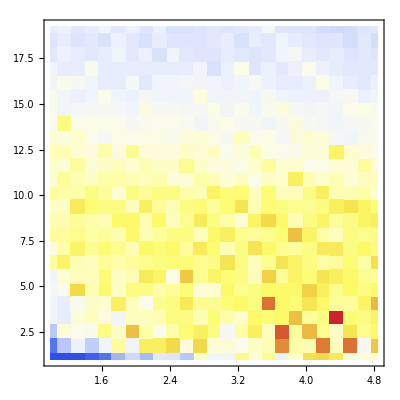
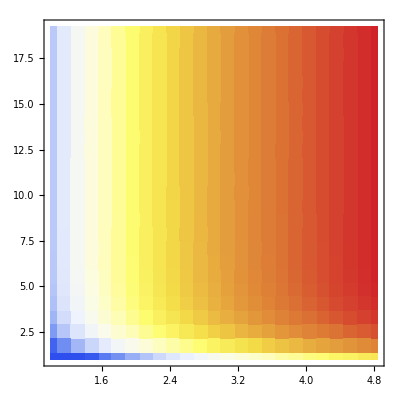
| (a)  Number of detectable species (> 10^-5) |  |  | (b)  Biomass (Total frequency of occupied sites) | 
 |  |  |  |  | 
    Magnitude of saturation    β | -Graphics- |  |  | -Graphics- | 
 |          Maximum fecundity    α |  |  |          Maximum fecundity    α |

```mathematica
frmopt[col_,fsize_]:={Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->Directive[{col,FontFamily->"Times New Roman",FontSize->fsize}]};
fstylopt[txt_,fsize_]:=Style[txt,Black,FontFamily->"Times New Roman",FontSize->fsize]

imgsize=280;
fig1=ListDensityPlot[dlist,Mesh->None,InterpolationOrder->0,ColorFunction->"TemperatureMap",PlotLegends->Automatic,Evaluate[frmopt[Black,12]],FrameLabel->None,ImageSize->{Automatic,imgsize}];
figl1=Append[fig1[[2]][[1]]//.{360->160, {}->Directive[{Black,FontFamily->"Times New Roman",FontSize->11}]},TicksStyle->Thickness[0.002]];

fig2=ListDensityPlot[blist,Mesh->None,InterpolationOrder->0,ColorFunction->"TemperatureMap",PlotLegends->Automatic,Evaluate[frmopt[Black,12]],FrameLabel->None,ImageSize->{Automatic,imgsize}];
figl2=Append[fig2[[2]][[1]]//.{360->160, {}->Directive[{Black,FontFamily->"Times New Roman",FontSize->11}]},TicksStyle->Thickness[0.002]];

g1=Grid[{{"",Item[fstylopt["(a)  Number of detectable species (> 10^-5)",15],Alignment->Left],"","",Item[fstylopt["(b)  Biomass (Total frequency of occupied sites)",15],Alignment->Left]},
{Spacer[{0,0}]},
{Item[Rotate[fstylopt["    Magnitude of saturation    β",14],Pi/2],Alignment->Center],fig1[[1]],figl1,Spacer[{0,0}],fig2[[1]],figl2},{"",fstylopt["         Maximum fecundity    α",14],"","",fstylopt["         Maximum fecundity    α",14]}},Alignment->Bottom];
Print[g1];
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_trade-off-para.pdf"],g1];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Figure is exported ...